## Hamilton equations for a basic system

q -> the coordinate 
qd = dq/dt

```mathematica
(*test function of the Hamiltonian*)
ham[n_,q_,qd_]:=4 qd^2*Sin[q]-Exp[q]+(n+1/2)*π*Sqrt[qd]; 
dhamq[n_,q_,qd_]:=D[ham[1,q,qd],q];
dhamq[n_,q_,qd_]:=D[ham[1,q,qd],qd];
```

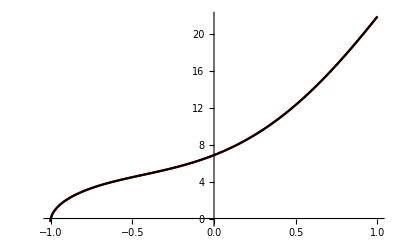

```mathematica
Show[Plot[ham[2,q,q+1],{q,-1,1},PlotStyle->Red],Plot[ham[2,q,q+1],{q,-1,1},PlotStyle->Black]]
```

General::ivar: 0.0000408571 is not a valid variable.

General::ivar: 0.0408572 is not a valid variable.

General::ivar: 0.0816735 is not a valid variable.

General::stop: Further output of General::ivar will be suppressed during this calculation.

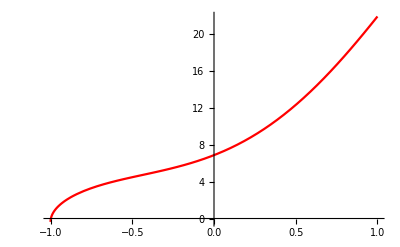

```mathematica
Show[Plot[ham[2,q,q+1],{q,-1,1},PlotStyle->Red],Plot[dhamq[2,q,q+1],{q,-1,1},PlotStyle->Black]]
```

```mathematica
D[ham[1,q,q+1],q]
```

-ⅇ^q+(3 π)/(4 √(1+q))+4 (1+q)^2 Cos[q]+8 (1+q) Sin[q]